```mathematica
Clear["Global`*"]
```

## Calculating parameters to couple light into a hollow core fiber

### Focusing light into fiber

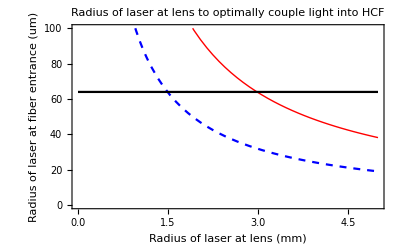

```mathematica
fiberRadius=100*10^-6;(*inner radius of fiber in m*)
wLegend =7.5/2*10^-3;(*measured 1/e^2 radius in m of Legend using DataRay camera*)
fIR=.75;(*focal length of lens in m*)
fBlue=1*fIR;
Mf[d_,f_]=({{1, d}, {0, 1}}).({{1, 0}, {-1/f, 1}});(*we focus beam into fiber entrance*)
q0[l_,w0_]=ⅈ*(π*w0^2)/l;(*q paramter of initial laser entering lens. We assume flat phase fronts, or infinite radius of curvature*)
qf[l_,d_,f_,w0_]=(Mf[d,f][[1,1]]*q0[l,w0]+Mf[d,f][[1,2]])/(Mf[d,f][[2,1]]*q0[l,w0]+Mf[d,f][[2,2]]);
w[l_,d_,f_,w0_]:=(-π/l Im[1/qf[l,d,f,w0]])^(-1/2);

Plot[{w[800*10^-9,fIR,fIR,w0*10^-3]*10^6,w[400*10^-9,fBlue,fBlue,w0*10^-3]*10^6,.64*fiberRadius*10^6},{w0,0,5},PlotRange->{0,100},Frame->True,FrameLabel->{"Radius of laser at lens (mm)","Radius of laser at fiber entrance (um)"},PlotLabel->"Radius of laser at lens to optimally couple light into HCF",PlotStyle->{{Red,Thick},{Blue,Dashed},Black}]
```

### Ideal Spot size

```mathematica
wi[l_,f_]:=Assuming[Element[w0,Reals]&&w0>0,Solve[w[l,f,f,w0]==.64*fiberRadius,w0]][[1,1,2]]//Quiet(*ideal radius of laser entering lens in m*)
factorIR=wi[800*10^-9,fIR]/wLegend//N(*magnification factor needed to reduce IR beam*)
factorBlue=wi[400*10^-9,fBlue]/wLegend//N; (*magnification factor needed to reduce Blue beam*)
(*{w[800*10^-9,fIR,fIR,.6*wLegend]*10^6,w[400*10^-9,fBlue,fBlue,.3*wLegend]*10^6}*)
wIR=wi[800*10^-9,fIR];
wBlue=wi[400*10^-9,fBlue];
wIR*1000
wBlue*1000
-{-30,-50,-75,-100}/factorIR (*required focal length of f1 given f2*)
```

0.795775

2.98416

1.49208

{37.6991,62.8319,94.2478,125.664}

```mathematica
(*Plot[wi[800*10^-9,f*10^-3]/wLegend,{f,500,1000},Frame->True,FrameLabel->{"Focal length (mm)","Reduction factor"},PlotStyle->{Red}]*)
```

```mathematica
(*Plot[{w[800*10^-9,d*10^-2,fIR,2*10^-3]*10^6,.64*fiberRadius*10^6},{d,0,fIR*10^2},PlotRange->{0,100},Frame->True,FrameLabel->{"Distance (cm)","Laser Radius (um)"},PlotStyle->{Red,Black}]
Plot[{w[400*10^-9,d*10^-2,fBlue,2*10^-3]*10^6,.64*fiberRadius*10^6},{d,0,fBlue*10^2},PlotRange->{0,100},Frame->True,FrameLabel->{"Distance (cm)","Laser Radius (um)"},PlotStyle->{Blue,Black}]*)
(*Plot3D[{w[800*10^-9,f*10^-3,f*10^-3,w0*10^-3]*10^6,.64*fiberRadius*10^6},{w0,0,5},{f,0,1000},AxesLabel->{"Input Laser Waist (mm)","Focal Length (mm)","Spot size at waist (um)"},PlotStyle->{Red,Black},PlotRange->{0,100}]
Plot3D[{w[400*10^-9,f*10^-3,f*10^-3,w0*10^-3]*10^6,.64*fiberRadius*10^6},{w0,0,5},{f,0,1000},AxesLabel->{"Input Laser Waist (mm)","Focal Length (mm)","Spot size at waist (um)"},PlotStyle->{Blue,Black},PlotRange->{0,100}]*)
```

### Intensity

{12.5,12.5}

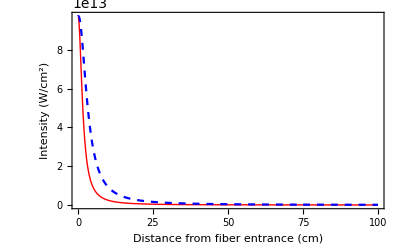

```mathematica
energy={.5,.5}*10^-3;(*energy in laser pulse in J, (pump,signal) *)
pd=40*10^-15;(*pulse duration in s*)
power = energy/pd;(*power in pulse in W*)
power*10^-9(*power in GW*)
int[p_,l_,z_,f_,w0_]=p/(π*w[l,z,f,w0]^2);(*intenisty in W/m^2*)
Plot[{int[power[[2]],800*10^-9,-z*10^-2+fIR,fIR,wIR]*10^-4,int[power[[1]],400*10^-9,-z*10^-2+fBlue,fBlue,wBlue]*10^-4},{z,0,100},Frame->True,FrameLabel->{"Distance from fiber entrance (cm)","Intensity (W/cm^2)"},PlotRange->All,PlotStyle->{{Red,Thick},{Blue,Dashed}}]
```

### B-Integral

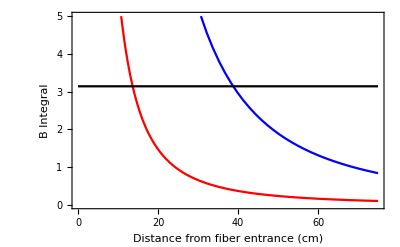

```mathematica
n2 = 1*10^-20;(*intensity dependent refractive index in m^2/W*)
length = 3*10^-3;(*length of window in m*)
B[p_,l_,z_,f_,w0_]:=(2π)/l*n2*Integrate[int[p,l,z,f,w0],{x,z,z+length}]

(*Plot[{B[power[[1]],400*10^-9,z*10^-2,fBlue,wi],B[power[[2]],800*10^-9,z*10^-2,fIR,wi],π},{z,0,fBlue*10^2},Frame->True,FrameLabel->{"Distance from lens (cm)","B Integral"}]
*)
Plot[{B[power[[1]],400*10^-9,-z*10^-2+fBlue,fBlue,wBlue],B[power[[2]],800*10^-9,-z*10^-2+fIR,fIR,wIR],π},{z,0,fIR*10^2},Frame->True,FrameLabel->{"Distance from fiber entrance (cm)","B Integral"},PlotRange->{0,5},PlotStyle->{Blue,Red,Black}]
```